# Cosmology Calculator

```mathematica
Clear["Global`*"];
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

-Graphics-

```mathematica
(*scale factor in terms of the Redshift  *)
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
```

-Graphics-

```mathematica
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
```

-Graphics-

```mathematica
(*Function to compute Physical time for a given redshift = (a'(tau))/a*)
time[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/((1+z)√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞}]
```

Friedmann equation: (FROM https://en.wikipedia.org/wiki/Hubble%27s_law)

-Graphics-

```mathematica
(*Physical Hubble Function at a given redshift = (ȧ)/a *)
PhysicalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Time derivative of the Conformal Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubble[z,H0,Ωm,Ωd,w,Ωr],z]*(-(1+z)^2)*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d HH)/dtau = dH/dz  dz/da da/dtau*)
```

```mathematica
(*(*Physical Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrimePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr],z]*D[1/a-1,a]*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d ^2HH)/dtau^2 = dH/dz  dz/da da/dtau*)*)
```

The equation to find a’’(\tau) which must be consistent with what we find previously. We don’t need to do it, instead we can just

Where for when we don’t have radiation:

-Graphics-

Here we neglect pressure from radiation, meaning that we don' t go deep to the radiation domination and we start our equations from z = 1000 for example

```mathematica
(*Here we neglect pressure from radiation, meaning that we don't go deep to the radiation domination and we start our equations from z=1000 for example*)

dNlnH[NN_,H0_,Ωm_,Ωd_,w_]:= D[ Log[ConformalHubble[1/E^NN-1,H0,Ωm,Ωd,w,0]],NN](*N=ln a*)
Psiequation[ψ_,NN_,H0_,Ωm_,Ωd_,w_]:= ψ''[NN] +(3+ dNlnH[NN,H0,Ωm,Ωd,w])ψ'[NN]+(2-(3 Ωm)/(2 Ωm + 2 Ωd Exp[-3w NN])+dNlnH[NN,H0,Ωm,Ωd,w])ψ[NN]
```

Finding Ψ fom the Growth factor equation

-Graphics--Graphics-

-Graphics-

```mathematica
Growthequation = DD''[τ] +a'[τ]/a[τ] DD'[τ]+-3/2 Ωm (a'[τ]/a[τ])^2 DD[τ];
```

Substituting the ansatz and then see if the equation we get is similar

```mathematica
Block[{DD},DD[τ_]:=Ψ[τ]a[τ];Growthequation]==0 /.{a'[τ]->Η[τ] a[τ]}/.{a''[τ]->Η'[τ]a[τ] + Η[τ]^2 a[τ]}//Simplify
```

a[τ] ((-4+3 Ωm) Η[τ]^2 Ψ[τ]-6 Η[τ] Ψ'[τ]-2 (Ψ[τ] Η'[τ]+Ψ''[τ]))==0

RESULTS

τ :  with high accuracy

```mathematica
(* Cosmology setting *)
H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-1;Ωd=1-Ωm-Ωr;
NumberForm[tau[0,H0,Ωm,Ωd,w,Ωr],12]
(*Ωd*)
```

tau[0,0.0691023,0.31,0.68991,-1,9/100000]

0.68991

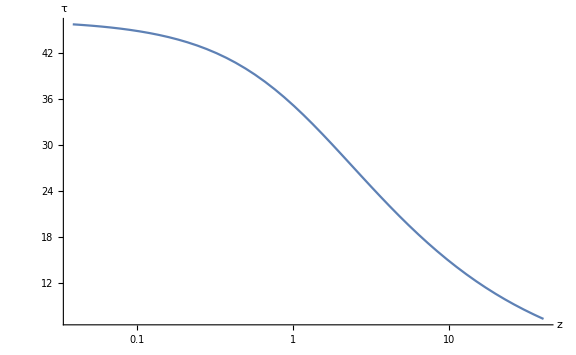

```mathematica
(* Cosmology setting *)
Ωd=0.687;H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-1;
LogLinearPlot[tau[z,H0,Ωm,Ωd,w,Ωr],{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for \HH(z)

-Graphics-

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

H0 √(Ωd (z+1)^(3 w+1)+Ωm (z+1)+Ωr (z+1)^2)

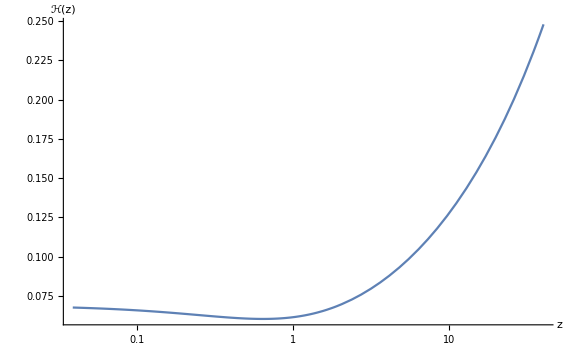

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for d \HH/dtau (z)

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

-1/2 H0^2 (z+1) ((3 w+1) Ωd (z+1)^(3 w)+Ωm+2 Ωr (z+1))

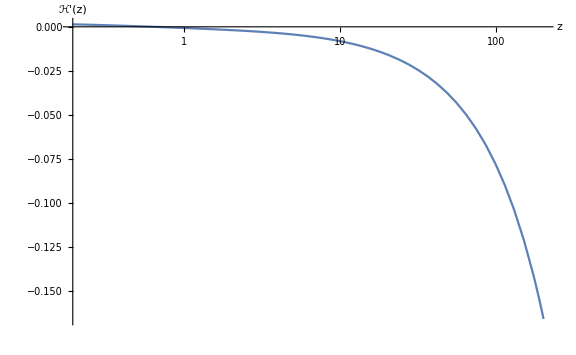

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,200},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ'(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
ConformalHubble[a_,H0_,Ωm_,Ωd_,ΩL_,w_,Ωr_]:=H0 √(Ωd(a)^(-(1+3 w)) + ΩL(a)^2+Ωm (a)^-1+Ωr(a)^-2)
```

```mathematica
Hprime = D[ConformalHubble[a,H0,Ωm,Ωd,ΩL,w,Ωr],a]*ConformalHubble[a,H0,Ωm,Ωd,w,Ωr]*a
```

1/2 a H0^2 (a^(-2-3 w) (-1-3 w) Ωd+2 a ΩL-Ωm/a^2-(2 Ωr)/a^3)

```mathematica
H0^2/(2 a^2)(-Ωm * a + 2 ΩL * a^4 -2 Ωr - (1 + 3 w ) Ωd a^(1- 3w)  ) == 1/2 a H0^2 (a^(-2-3 w) (-1-3 w) Ωd+2 a ΩL-Ωm/a^2-(2 Ωr)/a^3)//Simplify
```

True

```mathematica
D[Hprime,a]*ConformalHubble[a,H0,Ωm,Ωd,w,Ωr]*a//Simplify
```

```mathematica
1/2 a^(-2-3 w) H0^3 √((a^(1-3 w) Ωd+a^4 ΩL+a Ωm+Ωr)/a^2) (a (1+3 w)^2 Ωd+4 a^(4+3 w) ΩL+a^(1+3 w) Ωm+4 a^(3 w) Ωr)
```